In the limit ρ → 0 we assume ψ(i,a) = √(λ_(i',a'))ψ(i’,a’) where i’ and a’ are the renormalized indices afetr a decimation.

The goal of this Mathematica script is to test numerically whether such a scaling matrix λ_(i',a') exists, and to measure it.

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* periodic approximant of Fibonacci Hamiltonian, in the co-basis, k wavevector *)
h[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
ha[4,tw,ts]//MatrixForm
```

(0 | 0 | 0 | -tw | 0 | ts | 0 | 0
0 | 0 | 0 | 0 | tw | 0 | ts | 0
0 | 0 | 0 | 0 | 0 | tw | 0 | ts
-tw | 0 | 0 | 0 | 0 | 0 | tw | 0
0 | tw | 0 | 0 | 0 | 0 | 0 | tw
ts | 0 | tw | 0 | 0 | 0 | 0 | 0
0 | ts | 0 | tw | 0 | 0 | 0 | 0
0 | 0 | ts | 0 | tw | 0 | 0 | 0)

```mathematica
Simplify[h[Pi,4,tw,ts],Assumptions->{tw>0,ts>0}]//MatrixForm
```

(0 | 0 | 0 | -tw | 0 | ts | 0 | 0
0 | 0 | 0 | 0 | tw | 0 | ts | 0
0 | 0 | 0 | 0 | 0 | tw | 0 | ts
-tw | 0 | 0 | 0 | 0 | 0 | tw | 0
0 | tw | 0 | 0 | 0 | 0 | 0 | tw
ts | 0 | tw | 0 | 0 | 0 | 0 | 0
0 | ts | 0 | tw | 0 | 0 | 0 | 0
0 | 0 | ts | 0 | tw | 0 | 0 | 0)

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wfk[k_,n_]:=Block[{val,vec,ts=10.,tw=1.},
{val,vec}=Eigensystem[h[k,n,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

```mathematica
n=9;
dk=0.1;
krange=Range[0,Pi,dk];
wfklist=ParallelMap[Abs[wfk[#,n]]^2&,krange];
wfmoy=Mean[wfklist];
```

```mathematica
MatrixPlot[Abs[wfk[2 Pi]]^2,ColorFunction->"ThermometerColors"]
```

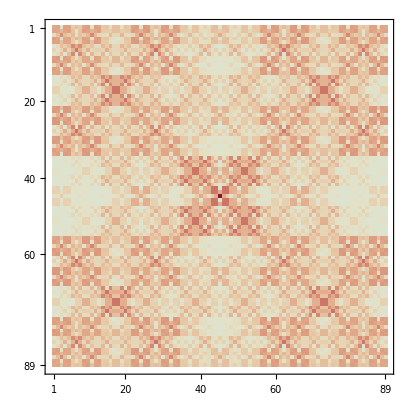
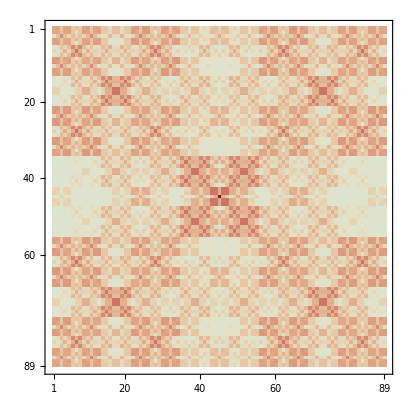

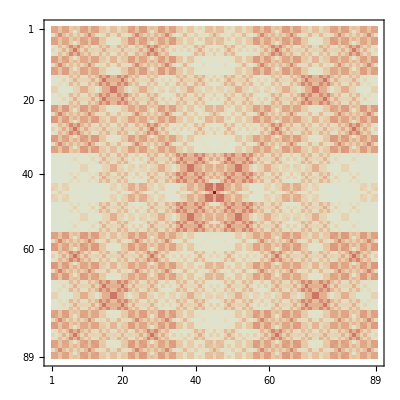

```mathematica
MatrixPlot[wfmoy,ColorFunction->"ThermometerColors"]
```

```mathematica
wfa=wfk[Pi];
```

```mathematica
wfp=wfk[0];
```

```mathematica
wf=wfk[Pi/2];
```

When ρ → 0, we see that the intensity on each of the 4 squares of size F_(n-2)×F_(n-2) is the same (perhaps up to a reflection). So, indeed, the intensity on each one of the 4 squares write I(i,a) = λ_(i',a') I(i’,a’), where I(i’,a’) is the intensity at step n-2.

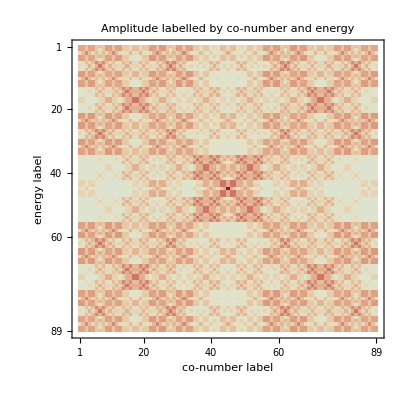

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->None,ColorFunction->"ThermometerColors"]
```

```mathematica
Plus@@#&/@(Abs[wf]^2)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

Measuring λ_(i',a')

```mathematica
(* system size *)
n=9;
nd=n-2;
(* coupling *)
ρ=1./10;

(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec},
{val,vec}=Eigensystem[h[Pi/2,n,ρ,1.]];
vec[[Ordering[val]]]
];
(* deflated wavefunctions *)
wfd=Block[{val,vec},
{val,vec}=Eigensystem[h[Pi/2,nd,ρ,1.]];
vec[[Ordering[val]]]
];
```

```mathematica
(* crop the square [1,Subscript[F, n-2]]×[1,Subscript[F, n-2]] *)
wfcropped=wf[[1;;Fibonacci[n],1;;Fibonacci[n]]];

(* crop the 3 remaining squares *)
(*wfcropped=wf[[1;;Fibonacci[n],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
wfcropped=wf[[Fibonacci[n+1]+1;;Fibonacci[n+2],1;;Fibonacci[n]]];
wfcropped=wf[[Fibonacci[n+1]+1;;Fibonacci[n+2],Fibonacci[n+1]+1;;Fibonacci[n+2]]];*)
```

```mathematica
dk=0.1;
krange=Range[0,Pi,dk];
wfklist=ParallelMap[Abs[wfk[#,n-2]]^2&,krange];
wfdmoy=Mean[wfklist];
```

```mathematica
wfmoycrop=wfmoy[[1;;Fibonacci[n],1;;Fibonacci[n]]];
```

```mathematica
(* λ matrix *)
MatrixPlot[wfmoycrop/wfdmoy,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListPlot3D[Abs[wfcropped/wfd]^2,InterpolationOrder->0,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(* λ matrix, having filtered to keep only sites having nonzero amplitude in the ρ = 0 limit *)
mask=Nest[recur,{m10,m20,m30,n0},n-5][[1]];
invMask=ConstantArray[1,{Fibonacci[n],Fibonacci[n]}]-mask;
filtWfCropped=wfcropped*mask+√0.5 invMask;
filtWfD=wfd*mask+invMask;
```

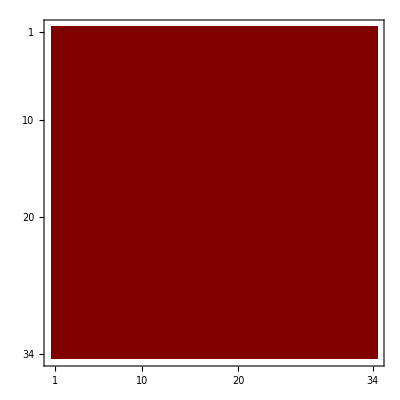

```mathematica
(* λ matrix *)
MatrixPlot[Abs[filtWfCropped/filtWfD]^2,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

```mathematica
ListPlot3D[Abs[filtWfCropped/filtWfD]^2,InterpolationOrder->0,PlotLegends->Automatic]
```

ListPlot3D::arrayerr: Abs[filtWfCropped/filtWfD]^2 must be a valid array or a list of valid arrays.

ListPlot3D[Abs[filtWfCropped/filtWfD]^2,InterpolationOrder→0,PlotLegends→Automatic]

```mathematica
(* crop the square [1,Subscript[F, n-2]]×[1,Subscript[F, n-2]] *)
wfcropped=wf[[1;;Fibonacci[n],1;;Fibonacci[n]]];

(* crop the 3 remaining squares *)
(*wfcropped=wf[[1;;Fibonacci[n],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
wfcropped=wf[[Fibonacci[n+1]+1;;Fibonacci[n+2],1;;Fibonacci[n]]];
wfcropped=wf[[Fibonacci[n+1]+1;;Fibonacci[n+2],Fibonacci[n+1]+1;;Fibonacci[n+2]]];*)
```

```mathematica
MatrixPlot [Abs[wfcropped]^2,ColorFunction->"ThermometerColors"]
```

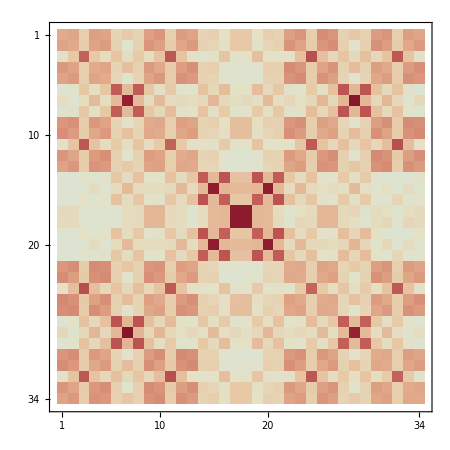
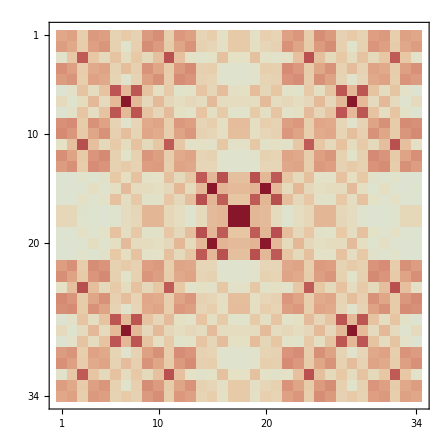

```mathematica
Transpose[tree[6]]//Last
```

{1/3,1/6,1/3,1/6,1/6,1/3,1/6,1/3}

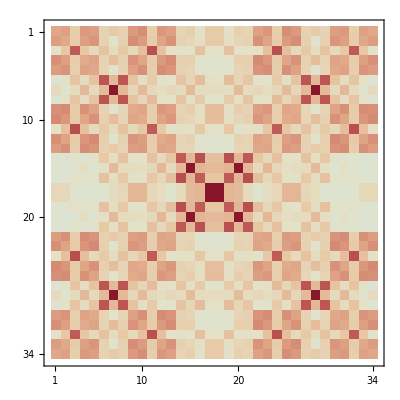

```mathematica
MatrixPlot [Abs[wfd]^2,ColorFunction->"ThermometerColors"]
```

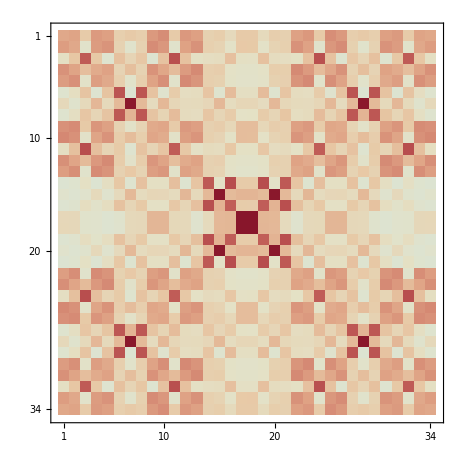
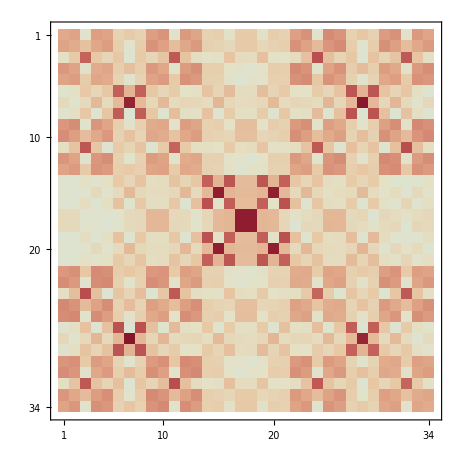

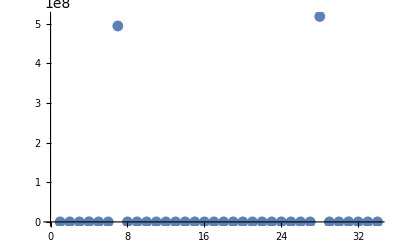

```mathematica
ListPlot[(Abs[wfcropped/wfd]^2)[[Fibonacci[n-3]-2]],PlotRange->All]
```